# Lecture 13 - Linking E⃗, ϕ, and ρ

### A Puzzle...

#### Inner-Surface Charge Density

A positive point charge q is located off-center inside a neutral conducting spherical shell. We know from Gauss’s law that the total charge on the inner surface of the shell is -q. Is the surface charge density negative over the entire inner surface? Or can it be positive on the far side of the inner surface if the point charge q is close enough to the shell so that it attracts enough negative charge to the near side? Justify your answer. 
Hint: Think about field lines.

```mathematica
centerPlot@-Graphics-
```

-Graphics-

Solution
If there were a location with positive density, then electric field lines would start there, pointing away from it into the spherical cavity. But where could these field lines end? They can’t end at infinity, because that’s outside the shell. And they can’t end at a point in empty space, because that would violate Gauss’s law; there would be nonzero flux into a region that contains no charge. They also can’t end on the positive point charge q, because the field lines point outward from q. And finally they can’t end on the shell, because that would imply a nonzero line integral of E⃗ (and hence a nonzero potential difference) between two points on the shell. But we know that all points on the conducting shell are at the same potential. Therefore, such a field line (pointing inward from the inner surface) can’t exist. So all of the inner surface charge must be negative. Every field line inside the cavity starts at the point charge q and ends on the shell. □

### A 30,000 Foot View (From Last Time)

It is important to realize that although we have been focusing specific charge distributions from points, lines, sheets, and spheres, electricity is one of the most prevalent and influential forces that we encounter in our daily lives! This remarkable YouTube video highlights some amazing electricity tricks that you can easily test out for yourself!

### Problems

#### Complementary Section: The Missing Link

By now, we are familiar with the three fundamental quantities in electrostatics, namely the:

Electric field (E⃗) - The electric field E⃗[r⃗] at a point r⃗ equals the force per unit charge that a point charge would feel at r⃗.

Electric potential (ϕ) - The potential ϕ[r⃗] equals the amount of work that must be done by an external agent in carrying a unit of positive charge from the reference point (usually infinity) to r⃗ without any acceleration.

Charge density (ρ) - The charge distribution everywhere.

These three quantities are connected by the following relations.

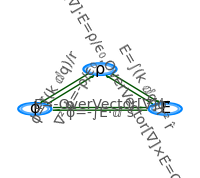

```mathematica
colors={RGBColor[0, 0.52, 1],RGBColor[Rational[1, 3], 0.6799999999999999, 1],GrayLevel[0.32],RGBColor[0, 0.33, 0]};
θ1=π/2;θ2=π/2+2π/3;θ3=π/2+4π/3;
p1={Cos[θ1],Sin[θ1]};p2={Cos[θ2],Sin[θ2]};p3={Cos[θ3],Sin[θ3]};
ft2=Style[#,14,FontFamily->"Times New Roman"]&;
s2=0.17;s3=0.9;
centerPlot@Graphics[{{colors[[1]],Thickness[0.008],Circle[#,0.22]&/@{p1,p2,p3}},{colors[[2]],Thickness[0.007],Circle[#,0.18]&/@{p1,p2,p3}},Text[font["ρ",16],p1],Text[font["ϕ",16],p2],Text[font["E⃗",16],p3],{colors[[4]],Arrow[1.1{{p1+s2(p2-p1),p2-s2(p2-p1)},{p3+s2(p2-p3),p2-s2(p2-p3)},{p1+s2(p3-p1),p3-s2(p3-p1)}}],Arrow[0.9{{p1+s3(p2-p1),p2-s3(p2-p1)},{p3+s3(p2-p3),p2-s3(p2-p3)},{p1+s3(p3-p1),p3-s3(p3-p1)}}]},Text[font["E⃗=-OverVector[∇]ϕ",colors[[3]]],(p2+p3)/2+{0,0.15}],Text[font["ϕ=-∫E⃗·ⅆ s⃗",colors[[3]]],(p2+p3)/2-{0,0.17}],Text[Rotate[font["∇^2 ϕ=-ρ/ϵ_0",colors[[3]]],Pi/3],(p1+p2)/2+{0.13,-0.18}],Text[Rotate[font["ϕ=∫(k ⅆq)/r",colors[[3]]],Pi/3],(p1+p2)/2+{-0.166,0.062}],Text[Rotate[font["E⃗=∫(k ⅆq)/r^2 r̂",colors[[3]]],-Pi/3],(p1+p3)/2+{0.172,0.09}],Text[Rotate[font["OverVector[∇]·E⃗=ρ/ϵ_0,OverVector[∇]×E⃗=OverVector[0]",colors[[3]]],-Pi/3],(p1+p3)/2+{-0.126,-0.15}]},ImageSize->200]
```

The only relation that we are not intimately familiar with is

∇^2 ϕ=-ρ/ϵ_0

which arises from combining E⃗=-OverVector[∇]ϕ together with ρ/ϵ_0=OverVector[∇]·E⃗=-OverVector[∇]·OverVector[∇]ϕ≡-∇^2 ϕ where we have defined the Laplacian

∇^2 ϕ=(∂ϕ)/(∂x^2)+(∂ϕ)/(∂y^2)+(∂ϕ)/(∂z^2)

in Cartesian coordinates. Surprisingly, Equation (TextNumbered) turns out to be one of the most useful relations in the diagram above because the Laplacian has many wonderful properties. For example, as discussed in class Equation (TextNumbered) in free space (ρ=0) becomes

∇^2 ϕ=0

whose solution ϕ[r⃗] equals the average value of ϕ in a small sphere around r⃗. This implies that ϕ has no minima or maxima, and therefore that you cannot construct an electrostatic field that will hold a charged particle in stable equilibrium. In more advances physics courses, this will be the primary problem solving tool in many electrostatics problems.

#### Complementary Section: Two Concentric Shells

Example
1. The shaded regions in the figure below represent two neutral concentric conducting spherical shells. The white regions represent vacuum. Two point charges q are located as shown; the interior one is off-center. Draw a reasonably accurate picture of the field lines everywhere, and indicate the various charge densities. What quantities are spherically symmetric? 
(As discussed in Exercise 3.49, there are two possible cases for what your picture can look like, depending on how close the exterior point charge is; take your pick.)

2. Repeat the above tasks in the case where the two shells are connected by a wire, so that they are at the same potential.

Solution
The charge distribution and field lines are shown (roughly) below. Let the surfaces be labeled 1, 2, 3, and 4 starting from the innermost one. There is charge -q on surface 1. This is true because the field is zero inside the metal of the conductor, so a spherical Gaussian surface drawn inside the metal of the inner conductor has no flux, and hence the net charge enclosed in the sphere must be zero. The negative surface charge density on surface 1 is higher near the off-center point charge. Since the inner conductor is neutral, a charge +q must reside on surface 2. This surface charge density is spherically symmetric, because it feels no field from the charges inside (or outside) of it, due to the zero field inside the metal of the conductors.)

By the same Gauss’s law reasoning, there must be a charge -q on surface 3, because there is zero field inside the metal of the outer conductor. The surface charge density is spherically symmetric. A charge +q is left for surface 4. This surface charge density is actually negative near the outer charge q if that charge is located close enough to the shells (see Exercise 3.49 for more details). But in any case, the total charge on surface 4 is +q. Between the shells, the field is spherically symmetric, consistent with the spherically symmetric charge densities on surfaces 2 and 3.

b) The shells are now at the same potential, so the field between them must be zero. Therefore, the only difference from the scenario in Part a is that we just need to erase the field between the shells and erase the charges on surfaces 2 and 3. The charges on surfaces 1 and 4 aren’t effected by this change, because the surfaces 2 and 3 together produced zero field everywhere except between them. □

#### Triangular E

Example
Find the charge density ρ and potential φ associated with the electric field shown in the figure below. E is independent of y and z. Assume that φ=0 at x=0.

```mathematica
centerPlot@-Graphics-
```

-Graphics-

Solution
Since E is independent of y and z, we should integrate ϕ=-∫E⃗[x]·ⅆs along the x-axis. Note that because the charge distribution goes out to infinity, we don’t set the zero potential at infinity (which would not be well defined), but instead use x=0. At a distance 0<x<a,

ϕ=-∫_0^x E[x̃]ⅆ x̃=-∫_0^x E_0(1-(x̃)/a)ⅆ x̃=-(E_0(x̃-(x̃)^2/(2a)))_(x̃=0)^(x̃=x)=E_0(x^2/(2a)-x)

For distances x>a, note that E[x]=0 for x>a so that ϕ[x]=ϕ[a] for this range. For x<0, we do a similar calculation to Equation (TextNumbered) above,

ϕ=-∫_0^x E[x̃]ⅆ x̃=-∫_0^x E_0(1+(x̃)/a)ⅆ x̃=-(E_0(x̃+(x̃)^2/(2a)))_(x̃=0)^(x̃=x)=-E_0(x^2/(2a)+x)

In summary,

ϕ=Piecewise[{{(E_0 a)/2, x<-a}, {-E_0(x^2/(2a)+x), -a≤x<0}, {E_0(x^2/(2a)-x), 0≤x<a}, {-(E_0 a)/2, a≤x}}]

The charge density ρ=-OverVector[∇]·E⃗=-(∂E)/(∂x). This is just a straightforward derivative which equals

ρ=Piecewise[{{0, x<-a}, {(ϵ_0 E_0)/a, -a≤x<0}, {-(ϵ_0 E_0)/a, 0≤x<a}, {0, a≤x}}]

This form of ρ shows us that the charge distribution is two infinity slabs with thickness a and opposite charge densities ±(ϵ_0 E_0)/a that touch at the x=0 plane. With this, we have a complete picture of the setup.

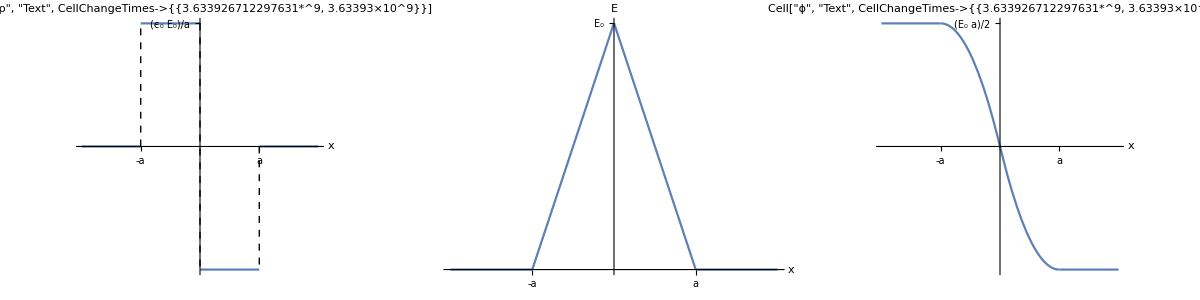

```mathematica
ρPlot=Show[Plot[{Piecewise[{{0,x<-1},{1,-1<x<0},{-1,0<x<1},{0,1<x}}]},{x,-2,2},Ticks->{{{1,"a"},{-1,"-a"}},{{1,"(ϵ_0 E_0)/a"}}},ImageSize->200,AxesLabel->{"x","Cell["ρ", "Text",
CellChangeTimes->{{3.633926712297631*^9, 3.63393×10^9}}]"}],Graphics[{Dashed,Line[{{-1,0},{-1,1}}],Line[{{0,1},{0,-1}}],Line[{{1,0},{1,-1}}]}]];
EPlot=Plot[{Piecewise[{{0,x<-1},{1+x,-1<x<0},{1-x,0<x<1},{0,1<x}}]},{x,-2,2},Ticks->{{{1,"a"},{-1,"-a"}},{{1,"E_0"}}},ImageSize->200,AxesLabel->{"x","E"}];
ϕPlot=Plot[{Piecewise[{{1/2,x<-1},{-x^2/2-x,-1<x<0},{x^2/2-x,0<x<1},{-1/2,1<x}}]},{x,-2,2},Ticks->{{{1,"a"},{-1,"-a"}},{{1/2,"(E_0 a)/2"}}},ImageSize->200,AxesLabel->{"x","Cell["ϕ", "Text",
CellChangeTimes->{{3.633926712297631*^9, 3.63393×10^9}}]"}];
centerPlot@Grid[{{ρPlot,EPlot,ϕPlot}}]
```

As a double check, at x=0 the two infinite slabs act effectively like sheets with charge densities ±σ=±ρ a. They create a field pointing to the right with magnitude σ/(2 ϵ_0), so the total field is 2(ρ a)/(2 ϵ_0)=(ρ a)/ϵ_0. Since we found that ρ=(ϵ_0 E_0)/a, the field equals E_0, in agreement with the given value. □

#### Satisfying Laplace

Example
Does the function f[x,y,z]=x^2+y^2 satisfy Laplace’s equation? Does the function g[x,y,z]=x^2-y^2?

Suppose g[x,y,z] represented an electric potential and that g[x,y,z] satisfies Laplace's equation. What can you say about the gradient OverVector[∇]g?

Solution
Here is a plot of f[x,y,z] and g[x,y,z].

```mathematica
centerPlot@Grid[{{Plot3D[x^2+y^2,{x,-5,5},{y,-5,5},PlotLabel->"f[x,y,z]=x^2+y^2",AxesLabel->Automatic,ImageSize->250],Plot3D[x^2-y^2,{x,-5,5},{y,-5,5},PlotLabel->"g[x,y,z]=x^2-y^2",AxesLabel->Automatic,ImageSize->250]}},Spacings->4]
```

-Graphics3D- | -Graphics3D-

In Cartesian coordinates, the Laplacian ∇^2 =⟨∂^2/(∂x^2),∂^2/(∂y^2),∂^2/(∂z^2)⟩. Therefore,

∇^2 f[x,y,z]=2+2≠0

does not satisfy Laplace’s equation while

∇^2 g[x,y,z]=2-2=0

does satisfy Laplace’s equation. If g[x,y,z] were an electrostatic potential, it would correspond to the electric field

-OverVector[∇]g[x,y,z]=⟨2x,-2y,0⟩

which is shown below for a constant z,

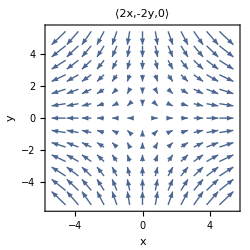

```mathematica
centerPlot@centerPlot@VectorPlot[{2x,-2y},{x,-5,5},{y,-5,5},ImageSize->250,FrameLabel->{"x","y"},PlotLabel->"⟨2x,-2y,0⟩",VectorPoints->13]
```

Because the Laplacian equals zero (or equivalently, the divergence of the gradient of g[x,y,z] equals zero), there is zero net flux out of any closed volume. You should convince yourself that this is true of the figure above. □

#### Complementary Section: Grounding a Shell

Example
A conducting spherical shell has charge Q and radius R_1. A larger concentric conducting spherical shell has charge -Q and radius R_2.

What is the potential at all points in space?

If the outer shell is grounded, explain why nothing happens to the charge on it.

If instead the inner shell is grounded, find its final charge.

Solution
Before either sphere is grounded, the electric field outside both spherical shells is zero, and hence the outer sphere has the same potential as infinity. This implies that when we ground the outer sphere, nothing will happen. If some negative charge did flow off, then there would be a net positive charge on the two shells, and hence an outward-pointing field for r>R_2, which would drag the negative charge back onto the outer shell. Similarly, if some positive charge flowed off, then there would be an inward-pointing field for r>R_2 which would drag the positive charge back onto the shell.

If the inner shell is grounded, it must end up with the amount of charge that makes its potential equal to the potential at infinity. Whatever charge distribution ultimately results must satisfy E=0 inside of both spherical conductors. Hence we know that there must be no charge on the inner surface of the smaller sphere, and all of the charge Q_1 on the smaller sphere must reside on its outer surface. The outer sphere must therefore have a charge -Q_1 on its inner surface (to satisfy E=0 inside), and hence the remaining charge Q_1-Q must be equally distributed on the outer surface of this larger sphere.

We can now calculate the potential everywhere. First, the potential ϕ[R_2] at the surface of the outer sphere must equal

ϕ[R_2]=(k(Q_1-Q))/R_2

since this is identical to the potential from a point charge Q_1-Q at the origin (using superposition). Next, the potential difference ϕ[R_1]-ϕ[R_2] between the inner sphere and the outer sphere equals

ϕ[R_1]-ϕ[R_2]=(k Q_1)/R_1-(k Q_1)/R_2

which is identical to the potential difference from a point charge Q_1 at the origin (by superposition and the fact that the charge Q_1-Q on the outer surface of the outer sphere generates no electric field for r<R_2). Therefore the potential ϕ[R_1] on the surface of the inner sphere, which must be zero at equilibrium, is given by

0=ϕ[R_1]=(k(Q_1-Q))/R_2+(k Q_1)/R_1-(k Q_1)/R_2

which we can solve to obtain

Q_1=R_1/R_2 Q

Intuitively, if none of the charge leaves (so Q_1=Q), then the inner shell is at a higher potential than the outer shell, which in turn is at the same potential as infinity in this case. On the other hand, if all of the charge leaves (so Q_1=0), then the inner shell is at the same potential as the outer shell, which in turn is at a lower potential than infinity in this case. So, by continuity, there must be a value of Q_1 that makes the potential of the inner shell equal to the potential at infinity.

#### Recommended Problems

This is a list of excellent problems (with solutions) in David Morin’s book.

3.10 Why leave?

### Advanced Section: Image Charges

#### Method of Images

Suppose the x-y plane is the surface of a conductor extending out to infinity. Let’s assign this plane the potential zero. Now bring in a positive charge Q and locate it z=h above the plane on the z-axis. How could we compute the electric field everywhere in space?

```mathematica
centerPlot@-Graphics-
```

-Graphics-

In other words, the constraints on this problem are that

V[x,y,0]=0

Lim_(r→∞)V[r]=0

By the Uniqueness Theorem, if we can come up with any charge configuration that has these properties, then it would have an identical solution to the above problem (aside from a small caveat discussed in the Note below).

The trick we will use is to consider a different scenario without the conducting plane where we have the same charge +Q at height z=h on the z-axis and an (imaginary) image charge -Q at height z=-h on the z-axis.

```mathematica
centerPlot@-Graphics-
```

-Graphics-

In this setup, the potential everywhere along the z=0 plane will have potential 0, and the potential will clearly fall off to zero infinitely far away (Lim_(r→∞)V[r]=0). Therefore, at any point for z≥0 in our original problem, the electric field is equal to that found using the image charge scenario for z≥0. For example, at the z=0 plane the electric field equals

E_z^above=-(2k Q)/(r^2+h^2)Cos[θ]
=-(2k Q)/(r^2+h^2)h/((r^2+h^2)^(1/2))
=-(2k Q h)/((r^2+h^2)^(3/2))

Note: This method is only valid for calculating the electric field at z>0 because we introduced the image charge at z=-h, in a region of space that is separated from z>0 region. You cannot introduce an image charge in the region z>0 and still claim that the electric field will be analogous in the two cases, because by introducing this image charge you have changed the problem. The image charge that we used in the above setup works because the image charge at z=-h performs the same function as the conducting plane, but only in the region z>0. (Mathematically speaking, the reason why the image charge scenario works at all is because of the Uniqueness Theorem, and in the wording of that theorem you will find see that it does not apply if you insert an image charge inside of your region of interest.)

For example, consider introducing an image charge -Q at a height z=h. This situation also satisfies equations (TextNumbered) and (TextNumbered). However, the resulting electric field (which is zero everywhere) clearly does not equal the electric field in our original problem for z≥0 (after all, near the point charge, there should be huge outward field). However, this situation could be used to compute the electric field for z<0 and show us that it is

E_z^below=0

Using the solution E_z^above in equation (TextNumbered) for z>0 and E_z^below for z<0 in equation (TextNumbered), we can compute the charge density σ everywhere on the surface of the conducting plate. Recall that σ/ϵ_0 is the difference in the electric field on either side of a plate,

σ=ϵ_0(E_z^above-E_z^below)=-(2 ϵ_0 k Q h)/((r^2+h^2)^(3/2))=-(Q h)/(2π (r^2+h^2)^(3/2))

```mathematica
centerPlot@-Graphics-
```

-Graphics-

We could integrate to calculate the total amount of charge on the surface

∫_0^∞ σ (2π r)ⅆr=-Q h ∫_0^∞ rⅆr/((r^2+h^2)^(3/2))=((Q h)/((r^2+h^2)^(1/2)))_(r=0)^(r=∞)=-Q

This result was to be expected. It means that all the flux leaving the charge Q ends on the conducting plane. It can also be explained by the fact that the image charge scenario required a total charge -Q placed below the surface to mimic the effects of the conducting plane.

#### Utilizing Image Charges

It is important to keep in mind that image charges are not real, which is why the analogy between the original setup and the image charge setup does not always work. For example, we that the image charges only allow us to determine the electric field for z>0. We could then use a different image charge scenario to compute the electric field for z<0.

By knowing the electric field at z>0, we can compute the force F⃗ on the charge +Q, and we find that it is identical to the force found in the image charge setup, namely F⃗=(k Q^2)/(2h)^2(-ẑ). We could compute the energy to bring the point charge Q from infinity to a height z=h, recalling that you apply a force F⃗ on the system,

U=∫_∞^h (-F⃗)·ⅆ l⃗=∫_∞^h (k Q^2)/(2z)^2 ⅆz=-(k Q^2)/(4h)

How does this compare to the work required to create the image charge setup? If we imagine first bringing in the image charge to z=-h and then bringing the real charge to z=h, the work would equal Q times the potential from the -Q image charge at a distance of 2h, namely Q (-(k Q)/(2h))=-(k Q^2)/(2h)=2U. Another way to think about this result is that you need to use energy U on both the real particle and the image particle as you bring them in from infinity. Why is this twice as large as the work done in our original problem?

In terms of force analysis, note that if you fix the conducting plate and bring in the charge from infinity, then the image charge is "brought in" from infinity for free, since the charges come in by moving on the conducting plate, which is an equipotential, so that it does not cost any work to move these charges about.

Another way to think about the energy result is by considering that the energy is stored in the electric field U=ϵ_0/2∫E^2 ⅆv, so that in the image charge problem there would be twice the energy (since E=0 for z<0 in the actual setup).

#### Horizontal Field Line

Example
In the field line of the point charge over the plane (shown above), if you follow a field line that starts out from the point charge in a horizontal direction, that is, parallel to the plane, where does it meet the surface of the conductor? (You’ll need Gauss’s law and a simple integration.)

Solution
Imagine a Gaussian surface which follows these horizontal field lines from the point charge all the way down to the conductor and then has a flat surface inside of the conductor (this shape is similar to a hemisphere). By construction, the electric field lines are parallel to the curved surface, so Gauss’s Law along that component will yield E⃗·ⅆ a⃗=0. Furthermore, on the flat portion inside of the conductor, E⃗=0 so that E⃗·ⅆ a⃗=0. Therefore, along this entire surface we find

∫E⃗·ⅆ a⃗=0=q_in/ϵ_0

This implies that the total charge inside of this Gaussian surface must be zero. We will approximate that 1/2 of the +Q point charge is inside of the Gaussian surface (if you like, imagine that the point charge is really a tiny sphere of charge in the limit that its radius goes to zero). This means that we need to integrate the charge distribution σ in equation (TextNumbered) to radius R so that the enclosed charge density is -Q/2, and then we will know where our Gaussian surface touches down upon the plane.

-Q/2=∫_0^R σ (2π r)ⅆr=-Q h ∫_0^R rⅆr/((r^2+h^2)^(3/2))=((Q h)/((r^2+h^2)^(1/2)))_(r=0)^(r=R)=(Q h)/((R^2+h^2)^(1/2))-Q

Solving this yields R=h √3.

This same method can easily be extended to compute where field lines starting at an angle θ from the vertical hit the conducting plate. As an exercise, you can show that this occurs at R=h ((3+2Cos[θ]-Cos[θ]^2)^(1/2))/(1-Cos[θ]). For θ=π/2, we recoup the answer R=h √3. For θ=0 and θ=π, we get R=∞ and R=0, as expected. For small θ=π-ϵ where ϵ≪1, we find R≈h ϵ/(√2). This is correctly smaller than the result h ϵ which would occur if the electric field used straight lines (as it must be, because the electric field lines have to curve in order to be vertical when they reach the conducting plane). I leave it as an exercise for you to determine why this √2 factor pops up.

In case you are worried about splitting the point charge in half, you can also setup your Gaussian surface to have a tiny spherical bump next to the point charge, as shown below.

```mathematica
centerPlot@-Graphics-
```

-Graphics-

In this case, we would expect that the total flux inside the Gaussian surface would be due to 1/2 of the flux from the point charge, and the solution would proceed accordingly.

#### Two Charges and a Plane

A positive point charge Q is fixed a distance l above a horizontal conducting plane. An equal negative charge -Q is to be located somewhere along the perpendicular dropped from Q to the plane. Where can -Q be placed so that the total force on it will be zero?

Solution
Denote the distance of the +Q and -Q charges as z=l and z=y, respectively. Since we want to find the electric field at z>0, we are allowed to use image charges provided we introduce them at z<0. One solution is to put an image charge +Q at z=-y and another charge -Q at z=-l.

```mathematica
centerPlot@-Graphics-
```

-Graphics-

The force on the charge -Q at z=y would equal

F⃗=k Q^2(1/(l-y)^2-1/(2y)^2+1/(l+y)^2)ẑ

Setting F⃗=OverVector[0] yields

0=1/(l-y)^2-1/(2y)^2+1/(l+y)^2

Getting a common denominator, this becomes a quadratic equation

0=(2y)^2(l+y)^2-(l-y)^2(l+y)^2+(2y)^2(l-y)^2=7 y^4+10 l^2 y^2-l^4

which yields

y^2=(-5±4 √2)/7 l^2

Only the positive root is physical, and we once again take a square root to find the solution

y=((-5+4 √2)/7)^(1/2)l≈0.306l

It may also be argued that setting y=l would yield another solution, since our equations indicate that the charge -Q would be quite happy there. Mathematically speaking, the infinite force that the particle would feel at that location is not considered stable; instead we are searching for locations where the electric field is zero. But physically speaking, when the two charges approach each other, the strong force would prevent them from overlapping, which would indeed cause a new equilibrium point very near to y≈l, but that topic goes beyond the range of this course. □

#### Recommended Problems

This is a list of excellent problems (with solutions) in David Morin’s book.

3.13 Image charge for a grounded spherical shell

## Mathematica Initialization

```mathematica
Clear[font]
font[text_,size_Integer:14,opts___]:=(Style[text,size,FontFamily->"Times",opts])
```